```mathematica
rmax=10.0;dr=0.25;
```

```mathematica
rlist=Range[0,rmax,dr]
```

{0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.,5.25,5.5,5.75,6.,6.25,6.5,6.75,7.,7.25,7.5,7.75,8.,8.25,8.5,8.75,9.,9.25,9.5,9.75,10.}

```mathematica
n=Length[rlist]
```

41

```mathematica
V[r_]:=1/2r^2
```

```mathematica
Vmat=DiagonalMatrix[V/@rlist];
```

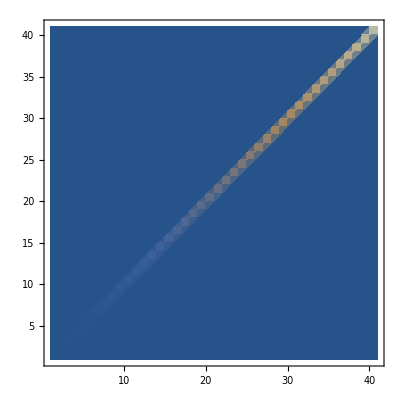

```mathematica
ListDensityPlot[Vmat]
```

```mathematica
(Tmat=RotateRight[IdentityMatrix[5]])//MatrixForm
```

(0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0)

```mathematica
Tmat[[1,5]]=0
```

0

```mathematica
Tmat//MatrixForm
```

(0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0)

```mathematica
RotateRight[{1,2,3}]
```

{3,1,2}

```mathematica
v=Interpolation[Transpose[{rlist,V/@rlist}]]
```

InterpolatingFunction[{{0., 10.}}, <>]

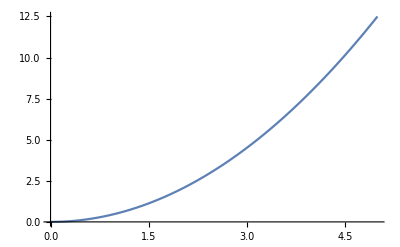

```mathematica
Plot[v[r],{r,0,5}]
```